# Bounds on ultralight bosons from the Event Horizon Telescope observation of Sgr A^* ( 2208.03530 ):

## Spin 0 ULB: (Refs. 1904.09242, 2009.07206, 2012.12790, 1908.10370)

```mathematica
G=6.708*10^-39 ;(* gravitational constant in GeV^-2, from PDG*)
rg[M_]:=G*(M *1.989*10^33*(5.62*10^23))*1/10^9 (*defined after Eq.3 of 2009.07206 ; Unit: eV^-1 ; Input mass in solar mass unit*)
rplus[a_,M_]:=rg[M](1+√(1-a^2)) (*defined below Eq.2 of 2009.07206*)
τ[t_]:=(t*3.156*10^7)/(6.582*10^-22*10^-3)*1/10^9 (*Unit: eV^-1 ; Input time in yr*)
dela[a_]:=1-a  (*defined above Eq.10 of 1904.09242*)
Nm[M_,a_,m_]:=1/m G*(M *1.989*10^33*(5.62*10^23))^2*dela[a] (*defined in Eq.4 of 1904.09242*)
Nmax[M_,a_]:=10^76*dela[a]/0.1*(M/10)^2(*defined in Eq.9 of 2009.07206*)
Omega[M_,a_]:=1/(2*rg[M])*a/(1+√(1-a^2))(*defined in Eq.2 of 1904.09242 ; Unit: eV*)
w[M_,mu_,n_,l_]:=mu*(1-1/2*((rg[M]*mu)/(n+l+1))^2)(*defined in Eq.6 of 2009.07206 *)
A[n_,l_]:=(2^(4l+1)(n+l)!)/((n-l-1)!n^(2l+4))((l!)/((2l)!(2l+1)!))^2(*defined in Eq.13 of 2009.07206 *)
χ[M_,a_,n_,l_,m_,mu_]:=Product[(k^2*(1-a^2)+(a*m-2*rplus[a,M]*w[M,mu,n,l])^2),{k,1,l}](*defined in Eq.14 of 2009.07206 *)
Γ[M_,a_,n_,l_,m_,mu_]:=2*(1+√(1-a^2))*(m*Omega[M,a]-w[M,mu,n,l])*(rg[M]*mu)^(4l+5)*A[n,l]*χ[M,a,n,l,m,mu] (*defined in Eq.12 of 2009.07206 *)(* extra factor of 2 taken, noted by Baumann et al., 1908.10370*)
μUpper[M_,a_]:=1/(2*rg[M])*a/(1+√(1-a^2))(*Upper limit on ULB mass constraint, defined in Eq. 5 of 1904.09242; Unit: eV*)
Γapprox0[a_,M_,mu_]:=1/48*a*(rg[M])^8*mu^9(*defined in Eq. 5 of 1904.09242, note the extra factor of 2 in the denominator*)
Solve0[M_,a1_,t_]:=μ/.NSolve[Γapprox0[a1,M,μ]*τ[t]==Log[Nm[M,a1,1]]&&μ>0,μ](*Solving the eqn for approximate expression of Γ*)
testSolve0[M_,a1_,t_]:=μ/.NSolve[Γ[M,a1,2,1,1,μ]*τ[t]==Log[Nm[M,a1,1]]&&rg[M]*μ<0.1&&μ>0,μ(*,Reals*)](*Solving the eqn for full expression of Γ*)
Γ[4*10^6,0.5,2,1,1,10^-18]
```

4.76857×10^-33

#### SgrA* Mass=4*10^6, a_*=0.94, τ=5*10^9 yr:

```mathematica
testSolve0[4*10^6,0.94,5*10^9]
Solve0[4*10^6,0.94,5*10^9]
μUpper[4*10^6,0.94]
```

{1.66865×10^-18}

{1.59237×10^-18}

1.16839×10^-17

#### SgrA* Mass=4*10^6, a_*=0.5, τ=5*10^9 yr:

```mathematica
testSolve0[4*10^6,0.5,5*10^9]
Solve0[4*10^6,0.5,5*10^9]
μUpper[4*10^6,0.5]
```

{1.85137×10^-18}

{1.71005×10^-18}

4.46682×10^-18

## Spin 1 ULB: (Refs. 1904.09242, 2009.07206, 2012.12790, 1908.10370)

```mathematica
B[n_,l_,j_]:=(2^(2l+2j+1)(l+n)!)/(n^(2l+4)(n-l-1)!)((l!)/((l+j)!(l+j+1)!))^2*(1+(2(1+l-j)(1-l+j))/(l+j))^2(*defined in Eq.17,18 of 2009.07206 *)
Y[M_,a_,n_,l_,j_,m_,mu_]:=Product[(k^2*(1-a^2)+(a*m-2*rplus[a,M]*w[M,mu,n,l])^2),{k,1,j}](*defined in Eq.19 of 2009.07206 *)

Γ2[M_,a_,n_,l_,j_,m_,mu_]:=2*(1+√(1-a^2))*(m*Omega[M,a]-w[M,mu,n,l])*(rg[M]*mu)^(2l+2j+5)*B[n,l,j]*Y[M,a,n,l,j,m,mu](*defined in Eq.16 of 2009.07206 *)
testSolve1[M_,a1_,t_]:=μ/.NSolve[Γ2[M,a1,1,0,1,1,μ]*τ[t]==Log[Nm[M,a1,1]]&&rg[M]*μ<0.1&&μ>0,μ](*Solving the eqn for full expression of Γ*)
Γapprox1[a_,M_,mu_]:=4*a*(rg[M])^6*mu^7  (*defined in Eq.6 of 1904.09242*)
Solve1[M_,a1_,t_]:=μ/.NSolve[Γapprox1[a1,M,μ]*τ[t]==Log[Nm[M,a1,1]]&&μ>0,μ](*Solving the eqn for approximate expression of Γ*)
```

#### SgrA* M=4*10^6, a_*=0.94, τ=5*10^9 yr

```mathematica
testSolve1[4*10^6,0.94,5*10^9]
Solve1[4*10^6,0.94,5*10^9]
μUpper[4*10^6,0.94]
```

{3.52124×10^-19}

{3.15101×10^-19}

1.16839×10^-17

#### SgrA* M=4*10^6, a_*=0.5, τ=5*10^9 yr

```mathematica
testSolve1[4*10^6,0.5,5*10^9]
Solve1[4*10^6,0.5,5*10^9]
μUpper[4*10^6,0.5]
```

{3.88643×10^-19}

{3.45352×10^-19}

4.46682×10^-18

## Spin 2 ULB: (Refs. 2009.07206, 2002.04055, 2012.12790)

```mathematica
Δ[a_]:=√(1-a^2) (*defined below Eq.24 of 2009.07206 *)
C1[M_,a_,n_,l_,j_,m_,mu_]:=(1+Δ[a])(Δ[a])^(2j)*Z[M,a,n,l,j,m,mu] (*defined in Eq.23 of 2009.07206 *)
Z[M_,a_,n_,l_,j_,m_,mu_]:=Product[(1+4(rg[M])^2*((w[M,mu,n,l]-m*Omega[M,a])/(k*Δ[a]*(1+Δ[a])^-1))^2),{k,1,j}] (*defined in Eq.24 of 2009.07206 *)
Γ3[M_,a_,n_,l_,j_,m_,mu_]:=(128/45)*(m*Omega[M,a]-w[M,mu,n,l])*(rg[M]*mu)^(2l+2j+5)*(C1[M,a,n,l,j,m,mu]/C1[M,0,n,l,j,m,mu]) (*defined in Eq.22,18 of 2009.07206 *)(* for 1022 mode , prefactor taken from https://journals.aps.org/prl/supplemental/10.1103/PhysRevLett.124.211101/spin2SR_SM.pdf*)
testSolve2[M_,a1_,t_]:=μ/.NSolve[Γ3[M,a1,1,0,2,2,μ]*τ[t]==Log[Nm[M,a1,1]]&&rg[M]*μ<0.1&&μ>0,μ](*Solving the eqn for full expression of Γ*)
Γapprox2[a_,M_,mu_]:=8*(a/(1+√(1-a^2)))*(rg[M])^8*mu^9  (*defined in Eq.3.7 of 2012.12790 *)
Solve2[M_,a1_,t_]:=μ/.NSolve[Γapprox2[a1,M,μ]*τ[t]==Log[Nm[M,a1,1]]&&μ>0,μ](*Solving the eqn for approximate expression of Γ*)
```

#### SgrA* M=4*10^6, a_*=0.94, τ=5*10^9 yr

```mathematica
testSolve2[4*10^6,0.94,5*10^9]
Solve2[4*10^6,0.94,5*10^9]
μUpper[4*10^6,0.94]
```

{8.81318×10^-19}

{8.49302×10^-19}

1.16839×10^-17

#### SgrA* M=4*10^6, a_*=0.5, τ=5*10^9 yr

```mathematica
testSolve2[4*10^6,0.5,5*10^9]
Solve2[4*10^6,0.5,5*10^9]
μUpper[4*10^6,0.5]
```

{1.04313×10^-18}

{9.46158×10^-19}

4.46682×10^-18

## Self-interaction bounds: (Refs. 2009.07206, 2012.12790)

```mathematica
Mpl=2.435*10^18;(* reduced Planck mass in GeV *)
Nbose[M_,mu_,f_,n_]:=5*10^94*n^4/(rg[M]*mu)^3(M/10^9)^2(f/Mpl)^2(* defined in Eq.4.2 of 2012.12790; f in GeV *)
μSLower[M_,a_,m_,t_]:=((48Log[Nm[M,a,m]])/(a*(rg[M])^8*τ[t]))^(1/9)(*defined in Eq. 8 of 1904.09242; Note the extra factor of 2; Unit: eV*)
Bound211=ParallelTable[{10^logμ,1/10^(Flatten[logfa/.NSolve[{Γ[4×10^6,0.94,2,1,1,10^logμ]×τ[5×10^9]×Nbose[4×10^6,10^logμ,10^logfa,2]/Nm[4×10^6,0.94,1]==Log[Nbose[4×10^6,10^logμ,10^logfa,2]]&&logfa≥0},logfa,Reals]][[1]])},{logμ,Log10[μSLower[4×10^6,0.94,1,5*10^9]],Log10[μUpper[4×10^6,0.94]],0.005}]  ;
Bound322=ParallelTable[{10^logμ,1/10^(Flatten[logfa/.NSolve[{Γ[4×10^6,0.94,3,2,2,10^logμ]×τ[5×10^9]×Nbose[4×10^6,10^logμ,10^logfa,3]/Nm[4×10^6,0.94,2]==Log[Nbose[4×10^6,10^logμ,10^logfa,3]]&&logfa≥0},logfa,Reals]][[1]])},{logμ,Log10[μUpper[4×10^6,0.94]],Log10[2*μUpper[4×10^6,0.94]],0.005}]  ;
Lowerlim=ParallelTable[{μSLower[4×10^6,0.94,1,5*10^9],10^g},{g,Log10[Bound211[[1]][[2]]],-18,-0.5}];
Upperlim1=ParallelTable[{μUpper[4×10^6,0.94],10^g},{g,Log10[Bound211[[-1]][[2]]],-18,-0.5}];
Upperlim2=ParallelTable[{2*μUpper[4×10^6,0.94],10^g},{g,Log10[Bound322[[-1]][[2]]],-18,-0.5}];
```

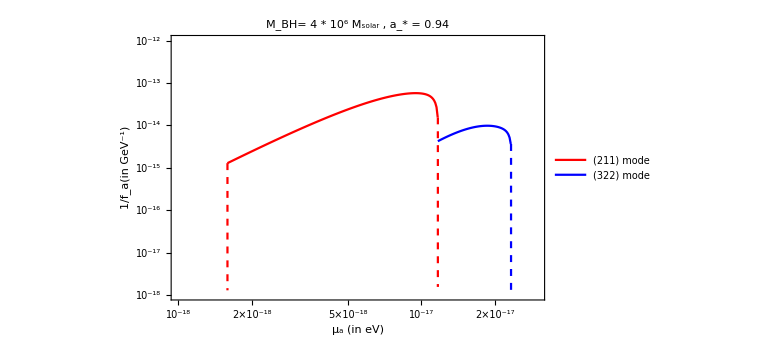

```mathematica
ListLogLogPlot[{Bound211,Bound322,Lowerlim,Upperlim1,Upperlim2},Joined->True,PlotRange->{{10^-18,3*10^-17},{10^-18,10^-12}},Frame->True,PlotStyle->{Red,Blue,{Red,Dashed},{Red,Dashed},{Blue,Dashed}},ImageSize->Large,PlotLegends->Placed[LineLegend[{Red,Blue},{"(211) mode","(322) mode"},LegendFunction->"Frame",LabelStyle->{FontSize->20,Black,FontFamily->"Latin Modern Roman"}],Automatic],FrameLabel->{"μ_a (in eV)","1/f_a(in GeV^-1)"},BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Directive[Black,Bold], PlotLabel->"M_BH= 4 * 10^6 M_solar ,  a_* = 0.94"]
```